# Efecto Hipster

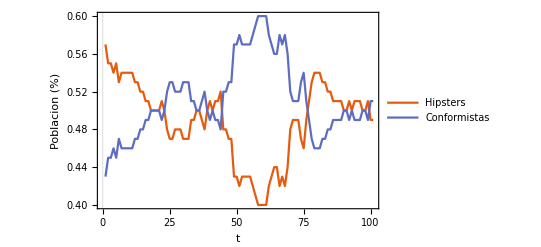

```mathematica
n= 100;
delay = 20;
hipsterFrac=0.4;
initialStateFrac = 0.5;
β = √10;

J =RandomVariate[ParetoDistribution[1,3], {n, n}]-0.5;
Do[J[[i,i]] = 0,{i,1,n}];
τ = 1+RandomVariate[PoissonDistribution[delay], {n, n}];
s = {ConstantArray[-1,n]+2*RandomChoice[{initialStateFrac, 1-initialStateFrac}->{1,0},n]};
ϵ = ConstantArray[-1,n]+2*RandomChoice[{hipsterFrac, 1-hipsterFrac}->{1,0},n];

ϕ[x_]:= (1+Tanh[β x])/2;
GetS[t_]:=If[t>0 &&t ≤ Length[s],
s[[t]],
s[[-1]]
];
Step[]:=Block[{m,ϕp,newS},
m = ParallelTable[1/n Sum[J[[i,j]]*GetS[Length[s]-τ[[i,j]]][[j]],{j,1,n}],{i,1,n}];
ϕp =ϵ *m *s[[-1]];
newS = s[[-1]]*Table[If[ϕp[[i]]>RandomReal[],-1,1],{i,1,n}];
AppendTo[s,newS];
];

Do[Step[],{100}]
hipters = Map[Count[#,1]&,s]/n;
conformist = Map[Count[#,-1]&,s]/n;

SetOptions[ListLinePlot,BaseStyle->{FontSize->14}];
ListLinePlot[{hipters,conformist},PlotRange->Full,FrameLabel->{"t","Poblacion (%)"},PlotTheme->"Scientific",PlotLegends->{"Hipsters", "Conformistas"}]
```

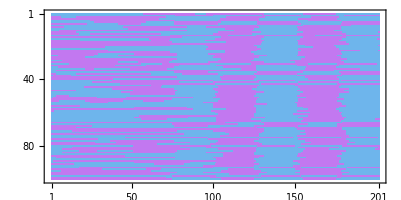

```mathematica
MatrixPlot[Transpose[s],ColorFunction->"Pastel"]
```